```mathematica
Quit[]
```

```mathematica
ClearAll["`*"]
```

# #1: Dark Sector Reheating

## Reheating of a Dark Sector (DS) from an early matter-dominated (EMD) era

Summary Report

Written by Manuel A. Buen-Abad, 2022

This is a notebook showing all the derivations of the quantities involved in computing the reheating of a Dark Sector (DS) via the decay of a reheaton ϕ, which dominates the Universe in an early matter-domination (EDM) era. The results of these derivations are hard-coded in the package DSReheating.wl.

## Preamble

## Directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Package

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

## Assumptions

```mathematica
$Assumptions=a>amin>0&&x>xmin>0&&wϕ>-1&&y>ymin>0&&γ>0&&γi>0&&γd>0&&f>1&&mPL>0&&gstar>0&&Arho>0
```

a>amin>0&&x>xmin>0&&wϕ>-1&&y>ymin>0&&γ>0&&γi>0&&γd>0&&f>1&&mPL>0&&gstar>0&&Arho>0

## Definitions

```mathematica
Clear[GeV,MeV,Mpl,mpl,second,Hz,mHz,h,ρcrit,H0,H0h1,Tγ0,gs0,ge0,gSM,Aρ,ρϕi]
```

### Units

```mathematica
GeV=1;
MeV=10^-3 GeV;
Mpl=1.22091 10^19 GeV;
mpl=Mpl/√(8π);
second=1.519268 10^21/MeV;
Hz=1/second;
mHz=10^-3 Hz;
```

### Constants

```mathematica
h=0.67;
ρcrit=8.0992*10^-47*h^2 GeV^4;
H0=√(ρcrit/(3 mpl^2));
H0h1=H0/h;

Tγ0=(2.4*10^-4)×10^-9 GeV;
gs0=3.94;
ge0=3.38;
gSM=106.75;
```

### Useful

```mathematica
Aρ=gstar π^2/30;
ρϕi=3 Hi^2 mpl^2;

gsdata=Import["./data/entropy_dof.csv"];
gsInt=Interpolation[gsdata,InterpolationOrder->1];
gsDomain=(gsInt//FullForm)⟦1,1⟧//Flatten;
gsFn[T_]:=Which[T<gsDomain⟦1⟧,gs0,T≤gsDomain⟦2⟧,gsInt[T],T>gsDomain⟦2⟧,gSM]
```

## For plots

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,color}"}]
Clear[fticksR,fticksR2,fticksR3,PrettyExp,PrettyExpR2,fticksRNoLabels,fticksR2NoLabels]
PrettyExp[x_,MAX_:2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]]
PrettyExpR2[x_,MAX_:2]:=If[Abs[x]>MAX,Superscript[10,2x],If[x≥0,10^x,10.^x]]
(* Axis for Epsilon versus mass: *)
fticksR[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
(* Axis for Epsilon versus mass, but with y-axis labels only every 2 decades *)
fticksR2[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]),10.^(1+x+Log[10,i-10])]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],2}],1]
(* Axis for Epsilon^2 versus mass *)fticksR3[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
(* Axis for Epsilon^2 versus mass, but with y-axis labels only every 2 decades *)
fticksR4[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]/2),10.^(0.5+x+Log[10,i-10]/2)]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1}],1]

fticksRNoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,"",{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
fticksR2NoLabels[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,"",{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,color}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
Clear[SciStr]
SciStr[x_,decimals_:0,latex_:False]:=Block[{X,pref,dex,scstr,string},

X=Log10[x];
dex=Floor[X];
pref=Round[(10^(X-dex))*10^decimals]*10^-decimals;

scstr=If[latex,StringReplace[ToString[StringForm["`1`\\times 10^(`2`)",pref,dex]],"`"->""],StringReplace[ToString[StringForm["`1`×10^(`2`)",pref,dex]],"\`"->""]];

string=If[MemberQ[{-1,0,1},dex],ToString[(Round[x*10^decimals]/10^decimals)//N],scstr];

string
]
```

## Reheating: Dark and Visible Sectors (DS & VS)

We will be solving for a two-fluid Universe: one a ϕ fluid that starts to decay at some time t_d (equivalently, scale factor a_d and Hubble scale H_d), and the other is made of the dark radiation decay products.

The evolution equations are:

(ρ̇)_ϕ+3H ρ_ϕ (1+w_ϕ)+Γρ_ϕ=0
(ρ̇)_r+4H ρ_r -Γρ_ϕ=0

It may be convenient to rewrite everything in dimensionless quantities, normalized to the value of ρ_(ϕ,d) at this time t_d when the decays start:

(1)   (d r_ϕ)/(d x)+3 h r_ϕ (1+w_ϕ)+γ r_ϕ=0
(d r_r)/(d x)+4 h r_r-γ r_ϕ=0

where we have defined

x≡t·H_d
H_d≡√((ρ_(ϕ,d))/(3 m_Pl^2))
r≡ρ/(ρ_(ϕ,d))
h≡H/H_d=√(r_ϕ+r_r)
γ_d≡Γ/H_d

with m_Pl being the reduced Planck mass: m_Pl≡M_Pl/(√(8π)).

Defining y≡ln(a/a_d) note that, since x≡t·H_d, then

(d y)/(d x)=1/a(d a)/(d t H_d)=1/H_d(ȧ)/a=H/H_d=h(y), and therefore:

x(y) = ∫_y_i^y (d y')/(h(y'))

where y=y_i corresponds to an initial scale factor a_i<<a_d. Note in particular that x(y=a)=H_d t(a_d)=H_d t_d is not necessarily equal to 1. This is because in the inverse of the Hubble expansion is not in general equal to time!

Defining A_ρ≡(π^2 g'_*)/30 then ρ_r=A_ρ T^4.

We can also define the factor f: ρ_(ϕ,d)≡f^4 ρ_(r,c), i.e. the initial ρ_ϕ in terms of ρ_r at the critical temperature. Thus, H_d^2=f^4(ρ_(r,c))/(3 m_Pl^2) and, since ρ_ϕ>ρ_r for all times:
ρ_ϕ>ρ_r ⇒ f^4 ρ_(r,c)=f^4 A_ρ T_c^4>A_ρ T^4⇒f>T/T_c, and in particular f>1.

⇒ r_r≡ρ_r/ρ_ϕ=ρ_r/(f^4 ρ_(r,c))=(T/(f T_c))^4, and r_(r,c)=f^-4.

## Numerical Solution

### Time as a function of scale factor: x(a)=H_d·t(a)

During reheaton-domination (ϕ-domination, with a constant equation of state w_ϕ), compute x(a) before the reheaton decays are allowed.

```mathematica
Clear[rϕNoDec,hNoDec,Dx,xOfa]
tempEqs={a D[rϕ[a],a]+3rϕ[a](1+wϕ)==0,rϕ[1]==1};
tempSols=DSolve[tempEqs,rϕ[a],a]//Flatten;

rϕNoDec=(rϕ[a]/.tempSols)//Simplify

hNoDec=√rϕNoDec//Simplify;

Dx=Assuming[aa>0,Integrate[(1/a)/hNoDec,a]//FullSimplify]/.aa->a
xOfa[wfi_,aa_]:=Block[{wϕ=wfi,a=aa},Dx]

Clear[tempEqs,tempSols,rϕNoDec,hNoDec]
```

a^(-3 (1+wϕ))

(2 a^((3 (1+wϕ))/2))/(3 (1+wϕ))

The (dimensionless) comoving time during reheaton domination, from x=0 to x(a=1):

(τ̄)_i≡∫_0^(x(a=1)) ⅆx'/(a(x')).

```mathematica
a/.(Solve[xOfa[wϕ,a]==x,a]//Flatten)
tauini=Integrate[1/%,{x,0,xOfa[wϕ,1]}]

taubarini[wfi_]:=Block[{wϕ=wfi},tauini]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(3/2)^(2/(3 (1+wϕ))) ((1+wϕ) x)^(2/(3 (1+wϕ)))

ConditionalExpression[2/(1+3 wϕ),wϕ>-1/3]

### Reheating Equations & Numerical Solution (in terms of x=t·H_d)

First, solving for rϕ at some x<xd at which the integration starts, by demanding that rϕ at x=0 is equal to 1. Since x<xd there are no decays yet.

```mathematica
Clear[hub,eqsX,solEqs]

(*decay time*)
xd=xOfa[wϕ,1];

(*dimensionless hubble*)
hub[x_]:=√(rϕ[x]+rr[x])

(*evolution equations (in terms of x=t*Hd).*)
eqsX={D[rϕ[x],x]+3hub[x]rϕ[x](1+wϕ)+γd rϕ[x]==0,D[rr[x],x]+4hub[x]rr[x]-γd rϕ[x]==0,rϕ[xd]==1,rr[xd]==0};

(*the solution to the system of equations*)
solEqs[gg_?NumberQ,wf_:0,xLarge_:10^3,prec_:30,accu_:20]:=solEqs[gg,wf,xLarge,prec,accu]=Block[{γd=Rationalize[gg],wϕ=wf,xmin,xmax,sols,dens,rϕd,hOfx,hd,res},

xmax=If[γd<1,Max[xLarge,100/gg],xLarge];

(*initial time*)
xmin=xd;

(*solving differential equations*)
sols=NDSolve[eqsX,{rϕ,rr},{x,xmin,xmax},WorkingPrecision->prec,AccuracyGoal->accu]//Flatten;

(*densities*)
dens={rϕ,rr}/.sols;

(*value of rϕ at x=xd*)
rϕd=dens⟦1⟧[xd];

(*h(x): dimensionless hubble as a function of x*)
hOfx=hub[x]/.{rϕ->dens⟦1⟧,rr->dens⟦2⟧};

(*h(1): dimensionless hubble at decay time a=1*)
hd=(hOfx/.{x->xd});

(*results*)
res={dens⟦1⟧,dens⟦2⟧}/.sols;

res
]
```

### Temperature T(x)

Computing the temperature as a function of time, assuming a certain Hubble scale H_scale and a certain number of degrees of freedom g_*.

```mathematica
Clear[TOfx]

TOfx[gg_?NumberQ,gs_,Hscale_,wf_:0,xLarge_:10^3,prec_:30,accu_:20]:=TOfx[gg,gs,Hscale,wf,xLarge,prec,accu]=Block[{gstar=gs,Hi=Hscale,wϕ=wf,rϕ,rr,xData,yData,data,Tfnx},

(*solving the reheating equations*)
{rϕ,rr}=solEqs[gg,wf,xLarge,prec,accu];

(*getting the temperature*)
xData=(InterpolatingFunctionCoordinates[rr]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[rr]//Flatten);
yData=((ρϕi*yData)/Aρ)^(1/4);

(*building the dataset*)
data={xData,yData}//Transpose;
Tfnx=Interpolation[data];

Tfnx
]
```

### Scale factor

Computing the scale factor as a function of time.

```mathematica
Clear[aOfx]

aOfx[gg_?NumberQ,aini_:1,sum_:False,wf_:0,xLarge_:10^3,prec_:30,accu_:20]:=aOfx[gg,aini,sum,wf,xLarge,prec,accu]=Block[{wϕ=wf,rϕ,rr,domain,xData,efolds,yData,data,afnx},

(*solving the reheating equations*)
{rϕ,rr}=solEqs[gg,wf,xLarge,prec,accu];

(*interpolation function properties*)
domain=(InterpolatingFunctionDomain[rr]//Flatten);
xData=(InterpolatingFunctionCoordinates[rr]//Flatten);

(*e-fold function*)
If[sum,
efolds[1]=0;
efolds[i_]:=efolds[i]=efolds[i-1]+((hub[xData⟦i⟧]+hub[xData⟦i-1⟧])/2)*(xData⟦i⟧-xData⟦i-1⟧),
efolds[1]=0;
efolds[i_]:=efolds[i]=efolds[i-1]+NIntegrate[hub[xx],{xx,xData⟦i-1⟧,xData⟦i⟧}]
];

(*computing e-folds*)
yData=Monitor[Table[efolds[i],{i,xData//Length}],ProgressIndicator[i,{1,xData//Length}]];
Clear[efolds];

(*computing scale factor*)
yData=aini*Exp[yData];

(*final data & interpolation*)
data={xData,yData}//Transpose;
afnx=Interpolation[data];

afnx
]
```

{9.47503,InterpolatingFunction[…]}

{0.075887,InterpolatingFunction[…]}

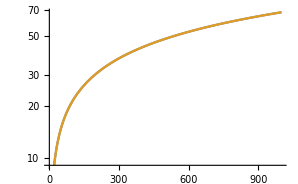

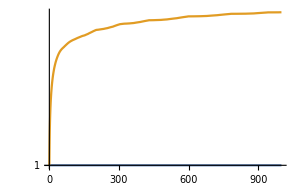

```mathematica
{time,afn1}=Timing[aOfx[0.1,1,False]]
dom=(InterpolatingFunctionDomain[afn1]//Flatten);
{time,afn2}=Timing[aOfx[0.1,1,True]]
LogPlot[{afn1[x],afn2[x]},{x,dom[[1]],dom[[2]]}]
LogPlot[{1,afn2[x]/afn1[x]},{x,dom[[1]],dom[[2]]}]

Clear[time,afn1,afn2,dom]
```

### Comoving time τ(x)

Computing the comoving time since x_i, with a given timescale t_scale:

τ(x)=t_scale((τ̄)_i+∫_x_i^x ⅆx'/(a(x'))).

```mathematica
Clear[tauOfx]

tauOfx[gg_?NumberQ,tscale_:1,aini_:1,sum_:False,wf_:0,xLarge_:10^3,prec_:30,accu_:20]:=tauOfx[gg,tscale,aini,sum,wf,xLarge,prec,accu]=Block[{wϕ=wf,ax,domain,xData,tau,yData,data,taufnx},

(*finding the scale factor a(x)*)
ax=aOfx[gg,aini,sum,wf,xLarge,prec,accu];

(*interpolation function properties*)
domain=(InterpolatingFunctionDomain[ax]//Flatten);
xData=(InterpolatingFunctionCoordinates[ax]//Flatten);

(*comoving time difference function*)
If[sum,
tau[1]=0;
tau[i_]:=tau[i]=tau[i-1]+((ax[xData⟦i⟧]^-1+ax[xData⟦i-1⟧]^-1)/2)*(xData⟦i⟧-xData⟦i-1⟧),
tau[1]=0;
tau[i_]:=tau[i]=tau[i-1]+NIntegrate[ax[xx]^-1,{xx,xData⟦i-1⟧,xData⟦i⟧}];
];

(*computing the comoving time difference*)
yData=Monitor[Table[tau[i],{i,xData//Length}],ProgressIndicator[i,{1,xData//Length}]];
Clear[tau];

(*adding initial comoving time and putting in the timescale*)
yData=tscale*(taubarini[wϕ]+yData);

(*final data & interpolation*)
data={xData,yData}//Transpose;
taufnx=Interpolation[data];

taufnx
]
```

{6.82732,InterpolatingFunction[…]}

{0.076426,InterpolatingFunction[…]}

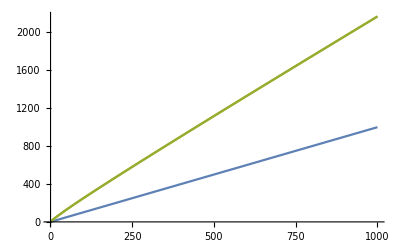

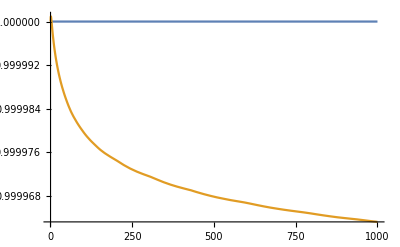

```mathematica
gam=0.1;
afn=aOfx[gam,1,False];
{time,tfn1}=Timing[tauOfx[gam,1,1,False]]
dom=(InterpolatingFunctionDomain[tfn1]//Flatten);
{time,tfn2}=Timing[tauOfx[gam,1,1,True]]

Plot[{x,afn[x]*tfn1[x],afn[x]*tfn2[x]},{x,dom[[1]],dom[[2]]}]

Plot[{1,tfn2[x]/tfn1[x]},{x,dom[[1]],dom[[2]]}]

Clear[gam,time,tfn1,tfn2,afn,dom]
```

### Redshift

We compute the total redshift (1+z) from today to the time when the GW were generated. For simplicity, it’s easier to start from the earliest times. We break the computation into three parts:
1. Redshift from GW generation until some time during the Dark Sector (DS) Radiation Domination (RD) era. Part of this process takes place during DS reheating (DSRH).
2. Redshift from this time until after the Visible Sector (VS) is reheated by the DS (VSRH).
3. Redshift from VSRH time until today.

For #1 the ratio (a(t_2))/(a(t_1))=(1+z_1)/(1+z_2) of scale factors between two times t_1<t_2 during DS reheating is simply equal to (a(t_2))/(a(t_1))=e^(∫_t_1^t_2 ⅆt  H(t))=e^(∫_x_1^x_2 ⅆx  h(x)).
For #2, VSRH can take place instantaneously or adiabatically. So we use either energy- or entropy-conservation as our guides.

```mathematica
Clear[redshift]

redshift[gg_?NumberQ,gs_,Hscale_,xRange_List,instant_,gdIRxiIRgIRTIR_List:{0,0,gSM,10^3},wf_:0,xLarge_:10^3,prec_:30,accu_:20,debug_:False]:=redshift[gg,gs,Hscale,xRange,instant,gdIRxiIRgIRTIR,wf,xLarge,prec,accu,debug]=Block[{gstar=gs,Hi=Hscale,wϕ=wf,xStar,xm,rϕ,rr,efolds,Tdm,gdIR,xiIR,gIR,TIR,Gfactor,Z1,Z2,Z3,res},

(*the time-range between GW production (x_*) and an arbitrary point during DS-RD era (Subscript[x, m])*)
{xStar,xm}=xRange;

(*computing the efolds between x_* and Subscript[x, m]*)
{rϕ,rr}=solEqs[gg,wf,xLarge,prec,accu];
efolds=NIntegrate[hub[x],{x,xStar,xm}];

(*the redshift factor between x_* and Subscript[x, m]*)
Z1=Exp[efolds];

(*computing the DS temperature at Subscript[x, m]*)
Tdm=TOfx[gg,gs,Hscale,wf,xLarge,prec,accu][xm];

(*VSRH (IR) quantities: DS d.o.f., DS-to-VS temperature ratio, VS d.o.f., VS temperature*)
{gdIR,xiIR,gIR,TIR}=gdIRxiIRgIRTIR;

(*computing the entropy dump from DS reheating the VS; whether instantaneously or adiabatically*)
Gfactor=If[instant,(gs/(gdIR*xiIR^4+gIR))^(1/4),(gs/(gdIR*xiIR^3+gIR))^(1/3)];

(*the redshift factor between Subscript[x, m] and Subscript[x, IR], at some arbitrary time shortly after VS reheating*)
Z2=Gfactor*Tdm/TIR;

(*the redshift factor from the time of VS reheating down until today*)
Z3=(gIR/gs0)^(1/3)*TIR/Tγ0;

(*the total redshift. Note that the explicit dependence on the VS temperature TIR after reheating from the DS cancels out; it only appears in gIR(TIR).*)
res=If[debug,{Z1*Z2*Z3,Z1,Z2,Z3},Z1*Z2*Z3];

res
]
```

#### Test

To double-check, we need to obtain the vanilla, traditional result. This is given by:

1. There is no DSRH (which can be mimicked by taking it to be extremely short).
2. There is actually no DS (which can be mimicked by taking T_d=T_SM and g_d=g_SM).

So to mimic this we search for a time at which T_d=100 GeV with g_d=100 (the benchmarks in the vanilla case). It doesn’t matter what Γ_d or H_d are, since we will take a vanishingly small redshift during DSRH.

For Γ=H_d=10*(1000 GeV)^2/m_Pl this time is x=151.45:

```mathematica
TOfx[1,100,10 1000^2/mpl][151.45]
```

100.001

We then compute the redshift from that time until today (note we take the xRange during DSRH to be vanishingly small). In terms of scale factor, we get a_*=8×10^-16, from the vanilla case.

```mathematica
redshift[1,100,10 1000^2/mpl,{151.45,151.45*(1+10^-6)},False]
%^-1
```

1.22451×10^15

8.16653×10^-16

Splitting the result into its various parts:

```mathematica
redshift[1,100,10 1000^2/mpl,{151.45,151.45*(1+10^-6)},False,{0,0,100,100},0,1000,30,20,True]
```

{1.22451×10^15,1.,1.00001,1.22449×10^15}

### Crossings

```mathematica
Clear[xCross]

xCross[gg_?NumberQ,rCrit_,wf_:0,xLarge_:10^3,prec_:30,accu_:20]:=xCross[gg,rCrit,wf,xLarge,prec,accu]=Block[{wϕ=wf,rϕ,rr,domain,xData,yData,xpk,xLSet,yLSet,xRSet,yRSet,xL0,xR0,xL,xR,eps=10^-4},

{rϕ,rr}=solEqs[gg,wf,xLarge,prec,accu];
domain=(InterpolatingFunctionDomain[rr]//Flatten);
xData=(InterpolatingFunctionCoordinates[rr]//Flatten);
yData=(InterpolatingFunctionValuesOnGrid[rr]//Flatten);

xpk=10^(LX/.FindMaximum[rr[10^LX]//Log10,{LX,0,Log10[domain⟦1⟧*(1+eps)],Log10[domain⟦2⟧]},MaxIterations->10^6,WorkingPrecision->prec]⟦-1⟧);

(*the initial guesses for the Left/Right crossing times*)
xLSet=Select[xData,(#<xpk)&];
yLSet=yData⟦1;;Length@xLSet⟧;
yLSet=Abs[yLSet-rCrit];
xL0=(Position[yLSet,Min[yLSet]]//Flatten)⟦1⟧;
xL0=xLSet⟦xL0⟧;

xRSet=Select[xData,(#>xpk)&];
yRSet=yData⟦(Length@yData-Length@xRSet)+1;;-1⟧;
yRSet=Abs[yRSet-rCrit];
xR0=(Position[yRSet,Min[yRSet]]//Flatten)⟦1⟧;
xR0=xRSet⟦xR0⟧;
Clear[xLSet,xRSet,yLSet,yRSet,xData,yData];

xL=10^(LX/.FindRoot[Log10[rr[10^LX]]==Log10[rCrit],{LX,Log10[xL0],Log10[domain⟦1⟧*(1+eps)],Log10[xpk]},MaxIterations->10^6,WorkingPrecision->prec]//Quiet);
xR=10^(LX/.FindRoot[Log10[rr[10^LX]]==Log10[rCrit],{LX,Log10[xR0],Log10[xpk],Log10[domain⟦2⟧*(1-eps)]},MaxIterations->10^6,WorkingPrecision->prec]//Quiet);

{xL,xpk,xR}
]
```

### Find rate γ

```mathematica
Clear[gammaRate]

gammaRate[gg_?NumberQ,xCrit_,wf_:0,δ_:10^-6,xLarge_:10^3,prec_:30,accu_:20]:=gammaRate[gg,xCrit,wf,δ,xLarge,prec,accu]=Block[{rϕ,rr,wϕ=wf,γ},

{rϕ,rr}=solEqs[gg,wf,xLarge,prec,accu];

γ=(xCrit-xd)/rr[xCrit]^(1/4)*(rr[(1+δ)xCrit]^(1/4)-rr[xCrit]^(1/4))/(δ xCrit);

γ
]
```

## Analytical Approximations

r_(r,c)≡r_r(x_c)=f^-4:

```mathematica
rrc=f^-4;
```

### Approximate Solutions & Useful Benchmarks

#### ϕD: reheaton domination (r_r<<r_ϕ)

In the equation for r_ϕ we simply ignore r_r:

```mathematica
DSolve[{rϕ'[x]+3 rϕ[x]^(3/2)==-γ rϕ[x],rϕ[2/3]==1},rϕ[x],x]
rϕSubSol={rϕ[x]->(ⅇ^(-γ(x-2/3)) γ^2)/((3 ⅇ^(-γ(x-2/3)/2)-3-γ)^2)}(*the non-singular solution, simplified*);
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rϕ[x]→(ⅇ^(2 γ/3) γ^2)/((3 ⅇ^(γ/3)-3 ⅇ^((x γ)/2)-ⅇ^((x γ)/2) γ)^2)},{rϕ[x]→(ⅇ^(2 γ/3) γ^2)/((3 ⅇ^(γ/3)-3 ⅇ^((x γ)/2)+ⅇ^((x γ)/2) γ)^2)}}

Substituting into the equation for r_r:

```mathematica
Assuming[γ>0&&x>2/3,({rr'[x]+4 rϕ[x]^(1/2)rr[x]==γ rϕ[x],rr[2/3]==0}/.rϕSubSol)//Simplify]
Assuming[γ>0&&x>2/3,DSolve[%,rr[x],x]//Simplify]//Flatten
rrSubSol={rr[x]->Assuming[γ>0&&x>2/3,(-1/(20 (-3+ⅇ^(1/6 (-2+3 x) γ) (3+γ))^(8/3)) ⅇ^(-11 γ/9) γ^2 (8 ⅇ^(1/3 (1+4 x) γ) (γ)^(5/3)+ⅇ^(1/3 (1+4 x) γ) (γ)^(5/3) γ-5 ⅇ^(11 γ/9) (-3+ⅇ^(1/6 (-2+3 x) γ) (3+γ))^(5/3)-3 ⅇ^((8 γ)/9+(x γ)/2) (-3+ⅇ^(1/6 (-2+3 x) γ) (3+γ))^(5/3)-ⅇ^((8 γ)/9+(x γ)/2) γ (-3+ⅇ^(1/6 (-2+3 x) γ) (3+γ))^(5/3)))//FullSimplify]}(*the real-valued solution *);
(*testing:*)
%%/.{γ->100.,x->1.}
rrSubSol/.{γ->100.,x->1.}
```

{(-3+ⅇ^(1/6 (-2+3 x) γ) (3+γ)) (4 γ rr[x]+(-3+ⅇ^(1/6 (-2+3 x) γ) (3+γ)) rr'[x])==γ^3,rr[2/3]==0}

{rr[x]→-(((-1)^(1/3) ⅇ^(-11 γ/9) γ^2 (8 ⅇ^(1/3 (1+4 x) γ) (-γ)^(5/3)+ⅇ^(1/3 (1+4 x) γ) (-γ)^(5/3) γ-5 ⅇ^(11 γ/9) (3-ⅇ^(1/6 (-2+3 x) γ) (3+γ))^(5/3)-3 ⅇ^((8 γ)/9+(x γ)/2) (3-ⅇ^(1/6 (-2+3 x) γ) (3+γ))^(5/3)-ⅇ^((8 γ)/9+(x γ)/2) γ (3-ⅇ^(1/6 (-2+3 x) γ) (3+γ))^(5/3)))/(20 (-3+ⅇ^(1/6 (-2+3 x) γ) (3+γ))^(8/3)))}

{rr[1.]→0.930349-3.38063×10^-14 ⅈ}

{rr[1.]→0.930349}

Putting them together: the solution rules, for r_ϕ>>r_r:

```mathematica
SubSol=rϕSubSol~Join~rrSubSol
```

{rϕ[x]→(ⅇ^(-(-2/3+x) γ) γ^2)/((-3+3 ⅇ^(-1/2 (-2/3+x) γ)-γ)^2),rr[x]→1/20 ⅇ^(-11 γ/9) γ^2 (-(ⅇ^(1/3 (1+4 x) γ) γ^(5/3) (8+γ))/((-3+ⅇ^(1/6 (-2+3 x) γ) (3+γ))^(8/3))+(5 ⅇ^(11 γ/9))/(-3+ⅇ^(1/6 (-2+3 x) γ) (3+γ))+(ⅇ^((8 γ)/9+(x γ)/2) (3+γ))/(-3+ⅇ^(1/6 (-2+3 x) γ) (3+γ)))}

These expressions are too complicated. It is convenient to split them into two cased depending on whether γ>>1 or γ<<1

```mathematica
Normal@Series[{rϕ[x],rr[x]}/.SubSol,{x,2/3,1}];
solsAn["γ>>1","ϕD"]={rϕ[x]->%⟦1⟧,rr[x]->%⟦2⟧}

Normal@Series[{rϕ[x],rr[x]}/.SubSol,{γ,0,1}];
solsAn["γ<<1","ϕD"]={rϕ[x]->%⟦1⟧,rr[x]->%⟦2⟧}
```

{rϕ[x]→1+(-2/3+x) (-3-γ),rr[x]→(-2/3+x) γ}

{rϕ[x]→4/(9 x^2)-(2 (-2+3 x) (2+3 x) γ)/(81 x^3),rr[x]→1/20 (-(32 (2/3)^(2/3))/(9 x^(8/3))+16/(3 x)) γ}

#### ϕR equality: r_eq≡r_r(x_eq)=r_ϕ(x_eq)

For the γ>>1 case they become equal shortly after the decays start

```mathematica
{rϕ[x],rr[x]}/.solsAn["γ>>1","ϕD"];
Solve[%⟦1⟧==%⟦2⟧,x]//Flatten
(%%/.%)⟦1⟧//Simplify
xEq["γ>>1"]=Normal@Series[x/.%%,{γ,∞,1}]
rEq["γ>>1"]=Normal@Series[%%,{γ,∞,1}]
```

{x→(9+4 γ)/(3 (3+2 γ))}

γ/(3+2 γ)

2/3+1/(2 γ)

1/2-3/(4 γ)

For the γ<<1 case this happens much later

```mathematica
Normal@Series[({rϕ[x],rr[x]}/.solsAn["γ<<1","ϕD"])/.x->1/t,{t,0,2}]/.t->1/x
xEq["γ<<1"]=x/.Assuming[0<γ<1,Solve[%⟦1⟧==%⟦2⟧,x,Reals]//Flatten]
rEq["γ<<1"]=(%%/.{x->%})⟦1⟧//Simplify
```

{4/(9 x^2)-(2 γ)/(9 x),(4 γ)/(15 x)}

10/(11 γ)

(22 γ^2)/75

#### RD: radiation domination (r_r>>r_ϕ)

Computing r_ϕ(x) in the r_r>>r_ϕ & γ>>1 limits

```mathematica
Assuming[γ>1&&x>2/3,DSolve[{rϕ'[x]==-γ rϕ[x],rϕ[xEq["γ>>1"]]==rEq["γ>>1"]},rϕ[x],x]//Simplify]//Flatten
(rϕ[x]/.%)
rϕSupSol={rϕ[x]->%}
```

{rϕ[x]→(ⅇ^(1/2+(2 γ)/3-x γ) (-3+2 γ))/(4 γ)}

(ⅇ^(1/2+(2 γ)/3-x γ) (-3+2 γ))/(4 γ)

{rϕ[x]→(ⅇ^(1/2+(2 γ)/3-x γ) (-3+2 γ))/(4 γ)}

Defining r_t≡r_ϕ+r_r:

r_t'(x)+4 r_t^(3/2)-4 r_t^(1/2)r_ϕ=0

Further defining y≡r_t^(1/2):
y'+2 y^2=2 r_ϕ=2 p^2 e^(-γ x);    with   p≡(e^(γ/3+1/4)((-3+2γ)/(4γ)))^(1/2).

```mathematica
(Assuming[γ>1&&x>2/3&&p>0,DSolve[{y'[x]+2 y[x]^2==p^2 Exp[-γ*x],y[xEq["γ>>1"]]==(2rEq["γ>>1"])^(1/2)},y[x],x]//Expand]//Flatten)/.p->((-3+2γ)/(2γ))*1/(√2)*E^(1/4)*Exp[γ/3](*p->((-3+2γ)/(4γ))^(1/2)*Exp[γ/3+1/4]*);
Assuming[k>0&&t>0&&x>2/3,(((y[x]/.%)/.γ->1/t))//FullSimplify]
temp=Assuming[k>0&&t>0&&x>2/3,Normal@Series[%,{t,0,1}]//FullSimplify]
```

-((ⅇ^((4+3 t-6 x)/(12 t)) (-2+3 t) (BesselI[1,ⅇ^((4+3 t-6 x)/(12 t)) t (-2+3 t)] (4 √(2-3 t) BesselK[0,(2-3 t) t]+√2 (-2+3 t) BesselK[1,(2-3 t) t])+(-4 √(2-3 t) BesselI[0,t (-2+3 t)]+√2 (-2+3 t) BesselI[1,(2-3 t) t]) BesselK[1,-ⅇ^((4+3 t-6 x)/(12 t)) t (-2+3 t)]))/(4 ((-4 √(2-3 t) BesselI[0,t (-2+3 t)]+√2 (-2+3 t) BesselI[1,(2-3 t) t]) BesselK[0,-ⅇ^((4+3 t-6 x)/(12 t)) t (-2+3 t)]+BesselI[0,ⅇ^((4+3 t-6 x)/(12 t)) t (-2+3 t)] (4 √(2-3 t) BesselK[0,(2-3 t) t]+√2 (-2+3 t) BesselK[1,(2-3 t) t]))))

((-2+3 t) (-3 ⅇ^(x/t) (4+5 t)-ⅇ^(1/2+2/(3 t)) t (2-12 x+t (-20+24 EulerGamma+21 x)+24 t Log[t])))/(16 ⅇ^(1/2+2/(3 t)) t^2 (-2+3 x)-4 ⅇ^(x/t) (2-12 x+t (4+3 x)))

```mathematica
Normal@Series[Numerator[#]&@temp,{t,0,1}]
Normal@Series[Denominator[#]&@temp,{t,0,1}]
Normal@Series[(%%/%)//Simplify,{t,0,0}]/.t->1/γ

rrSupSol={rr[x]->(%^2-0rϕ[x]/.rϕSupSol)//FullSimplify}
```

ⅇ^(x/t) (24-6 t)-4 ⅇ^(1/2+2/(3 t)) t (-1+6 x)

ⅇ^(x/t) (-4 (2-12 x)-4 t (4+3 x))

-6/(2-12 x)

{rr[x]→9/(1-6 x)^2}

The solution rules, for r_r>>r_ϕ and γ>>1

```mathematica
solsAn["γ>>1","RD"]=rϕSupSol~Join~rrSupSol
Clear[temp]
```

{rϕ[x]→(ⅇ^(1/2+(2 γ)/3-x γ) (-3+2 γ))/(4 γ),rr[x]→9/(1-6 x)^2}

Now for the γ<<1 limit

```mathematica
Assuming[γ>1&&x>2/3&&p>0,DSolve[{rr'[x]+4 rr[x]^(3/2)==0,rr[xEq["γ<<1"]]==rEq["γ<<1"]},rr[x],x]⟦2⟧]//Flatten//FullSimplify
Assuming[γ>1&&x>2/3&&p>0,DSolve[{rϕ'[x]+3(rr[x]/.%)^(1/2)rϕ[x]==-γ rϕ[x],rϕ[xEq["γ<<1"]]==rEq["γ<<1"]},rϕ[x],x]]//Flatten//FullSimplify
Normal@Series[rr[x]/.%%,{x,∞,2}];
Normal@Series[rϕ[x]/.%%,{x,∞,2}]//Simplify;
solsAn["γ<<1","RD"]={rϕ[x]->%,rr[x]->%%}
```

{rr[x]→(484 γ^2)/(5 (-8+√66)+44 x γ)^2}

{rϕ[x]→(22 22^(3/4) ⅇ^(10/11-x γ) γ^2)/(3^(1/4) √5 (5 (-8+√66)+44 x γ)^(3/2))}

{rϕ[x]→((11/6)^(1/4) ⅇ^(10/11-x γ) √(γ/x^3))/(2 √5),rr[x]→1/(4 x^2)}

#### L_r≡1/4(d ln r_r)/(d x)=(d ln T)/(d x)

Computing L_r≡1/4(d ln r_r)/(d x):

```mathematica
Do[Do[Lr[γRegime,era]=1/4 D[Log[rr[x]/.solsAn[γRegime,era]],x]//Expand//Simplify//FullSimplify,{γRegime,{"γ<<1","γ>>1"}}],{era,{"ϕD","RD"}}]
```

```mathematica
?Lr
```

#### Maximum: r_(r,max)≡r_r(x_max)

For γ<<1 it occurs during ϕD:

```mathematica
xMax["γ<<1"]=x/.(Solve[Lr["γ<<1","ϕD"]==0,x]//Flatten)
%/(2/3(8/3)^(3/5))
rrMax["γ<<1"]=((rr[x]/.solsAn["γ<<1","ϕD"])/.x->xMax["γ<<1"])//FullSimplify
%/(2/3(3/8)^(8/5)γ)
```

(4 2^(4/5))/(3 3^(3/5))

1

(3^(3/5) γ)/(8 2^(4/5))

1

For γ>>1 it occurs somewhere between ϕD & RD, so we need to combine both regimes

```mathematica
combined=(1/(rr[x]/.solsAn["γ>>1","ϕD"])+1/(rr[x]/.solsAn["γ>>1","RD"]))^-1;
1/4 D[Log[combined],x]//Simplify

Numerator[%];
(x/.#&)/@Solve[%==0,x];
(Normal@Series[#,{γ,∞,1}]&/@%)//FullSimplify//Expand

(*selecting the only solution with x>2/3, as is necessary*)
Normal@Series[%,{γ,1,1}](*it's enough to expand γ above 1 to check this out*);
Assuming[γ>1,Select[%,#>2/3&]]⟦1⟧(*the result must be larger than 2/3*);
Position[%%,%](*selecting the correct element from the list*);

xMax["γ>>1"]=(%%%%⟦(%//Flatten)⟦1⟧⟧)(*the full x solution*)
rrMax["γ>>1"]=Normal@Series[(combined/.{x->xMax["γ>>1"]})//FullSimplify,{γ,∞,1}]

Clear[combined]
```

(81-12 (2-3 x)^2 (-1+6 x) γ)/(4 (-2+3 x) (27+(1-6 x)^2 (-2+3 x) γ))

{1/6+1/(2 γ),2/3-1/(4 γ)+1/(2 √γ),2/3-1/(4 γ)-1/(2 √γ)}

2/3-1/(4 γ)+1/(2 √γ)

1+15/γ-4/(√γ)

### Reheating quantities at critical temperature

#### r_(r,c)≡r_r(x_c)

Now we search for x_c & r_(r,c). There’s always two solutions for x_c. Also, it is important to keep in mind that we will assume r_(r,c) is close to r_(r,max), which translates into a condition for the smallest allowed f: f_min(γ)

```mathematica
Solve[rrMax["γ<<1"]==rrc,f]
%//N
Solve[rrMax["γ>>1"]==rrc,f]
%//N
```

{{f→-2^(19/20)/(3^(3/20) γ^(1/4))},{f→-(ⅈ 2^(19/20))/(3^(3/20) γ^(1/4))},{f→(ⅈ 2^(19/20))/(3^(3/20) γ^(1/4))},{f→2^(19/20)/(3^(3/20) γ^(1/4))}}

{{f→-1.63836/γ^(1/4)},{f→-(0.+1.63836 ⅈ)/γ^(1/4)},{f→(0.+1.63836 ⅈ)/γ^(1/4)},{f→1.63836/γ^(1/4)}}

{{f→-γ^(1/4)/(15-4 √γ+γ)^(1/4)},{f→-(ⅈ γ^(1/4))/(15-4 √γ+γ)^(1/4)},{f→(ⅈ γ^(1/4))/(15-4 √γ+γ)^(1/4)},{f→γ^(1/4)/(15-4 √γ+γ)^(1/4)}}

{{f→-(1. γ^(1/4))/(15.-4. √γ+γ)^(1/4)},{f→-((0.+1. ⅈ) γ^(1/4))/(15.-4. √γ+γ)^(1/4)},{f→((0.+1. ⅈ) γ^(1/4))/(15.-4. √γ+γ)^(1/4)},{f→γ^(1/4)/(15.-4. √γ+γ)^(1/4)}}

Now let us find x_c1 & x_c2.

For γ<<1, x_c1 & x_c2 are both during ϕD. Since 2/3<x_c1<x_max≈1 then the first one lies somewhere after 2/3, whereas the other one lies when x>1

```mathematica
xc1=(x/.Solve[Normal@Series[((rr[x]/.solsAn["γ<<1","ϕD"])),{x,2/3,1}]==rrc,x]//FullSimplify//Flatten)⟦1⟧;
xc2=(x/.Solve[Normal@Series[((rr[x]/.solsAn["γ<<1","ϕD"])),{x,∞,1}]==rrc,x]//FullSimplify//Flatten)⟦1⟧;

xcVals["γ<<1"]={xc1,xc2}

Clear[xc1,xc2]
```

{2/3+1/(f^4 γ),(4 f^4 γ)/15}

For γ>>1 x_c1 occurs during ϕD, whereas x_c2 during RD

```mathematica
xc1=(x/.Solve[(rr[x]/.solsAn["γ>>1","ϕD"])==rrc,x]//FullSimplify//Flatten)⟦1⟧

(x/.Solve[(rr[x]/.solsAn["γ>>1","RD"])==rrc,x]//FullSimplify//Flatten)(*two solutions, need to pick up the positive one*)
Select[(%/.f->2),#>0&]⟦1⟧(*it's enough to check for a specific value of f, say f=2*);
Position[(%%/.f->2),%](*selecting the correct element from the list*);
xc2=(%%%⟦(%//Flatten)⟦1⟧⟧)(*the full xc2 solution*);

xcVals["γ>>1"]={xc1,xc2}

Clear[xc1,xc2]
```

2/3+1/(f^4 γ)

{1/6 (1-3 f^2),1/6 (1+3 f^2)}

{2/3+1/(f^4 γ),1/6 (1+3 f^2)}

#### L_(r,c)≡L_r(x_c)=1/4((d ln r_r)/(d x))_x_c

```mathematica
xcVals["γ<<1"]
LrcVals["γ<<1"]=Normal@Series[((Lr["γ<<1","ϕD"]/.x->#&)/@xcVals["γ<<1"])/.{f->(f4γ/γ)^(1/4)},{f4γ,∞,1}]/.f4γ->f^4 γ
```

{2/3+1/(f^4 γ),(4 f^4 γ)/15}

{-7/8+67/(48 f^4 γ)+(f^4 γ)/4,-15/(16 f^4 γ)}

```mathematica
xcVals["γ>>1"]
LrcVals["γ>>1"]={(Normal@Series[(Lr["γ>>1","ϕD"]/.x->xcVals["γ>>1"]⟦1⟧)/.{f->(f4γ/γ)^(1/4)},{f4γ,∞,1}]/.f4γ->f^4 γ),Lr["γ>>1","RD"]/.x->xcVals["γ>>1"]⟦2⟧}
```

{2/3+1/(f^4 γ),1/6 (1+3 f^2)}

{(f^4 γ)/4,-1/f^2}

#### H_c≡H(x_c)=H_dec √(r_ϕ+r_r)

For γ<<1, both x_(c,1/2) occur during ϕD:

```mathematica
(rϕ[x]/.solsAn["γ<<1","ϕD"])
xcVals["γ<<1"]
```

4/(9 x^2)-(2 (-2+3 x) (2+3 x) γ)/(81 x^3)

{2/3+1/(f^4 γ),(4 f^4 γ)/15}

For x_c1≈2/3, we find r_(ϕ,c1)≈1

```mathematica
(rϕ[x]/.solsAn["γ<<1","ϕD"]);
Normal@Series[%,{x,2/3,1}](*for Subscript[x, c1]≈2/3*);
%/.x->xcVals["γ<<1"]⟦1⟧
```

1+(-3-γ)/(f^4 γ)

For x_c2, we find that the dominant term goes like r_(ϕ,c2)≈(5/2 1/(f^4 γ))^2:

```mathematica
((rϕ[x]/.solsAn["γ<<1","ϕD"])/.x->xcVals["γ<<1"]⟦2⟧)//Expand

(*check*)
g0=0.01;
%%/.{γ->g0};
{(7.2/g0)^(1/4),(3.3/g0^2)^(1/4)}
(%%/.f->#)&/@%

(25/(4 f^8 γ^2)/.{γ->g0,f->#})&/@%%
Clear[g0]
```

-5/(6 f^4)+125/(24 f^12 γ^2)+25/(4 f^8 γ^2)

{5.18004,13.4781}

{0.119545,0.000032141}

{0.120563,0.0000573921}

For γ>>1 x_c1 occurs during ϕD, x_c2 during RD

```mathematica
xcVals["γ>>1"]
(rϕ[x]/.solsAn["γ>>1","ϕD"])/.{x->%⟦1⟧}
(rr[x]/.solsAn["γ>>1","RD"])/.{x->%%⟦2⟧}
```

{2/3+1/(f^4 γ),1/6 (1+3 f^2)}

1+(-3-γ)/(f^4 γ)

1/f^4

So putting everything together:

```mathematica
HdecFactor=Assuming[Arho>0&&mPL>0,√(f^4 Arho/3 Tc^4/mPL^2)//Simplify];
HcVals["γ<<1"]=(HdecFactor*{√1,√(25/4*1/(f^8 γ^2))})//Simplify;
HcVals["γ>>1"]=(HdecFactor*{√1,√(f^-4)//Simplify})//Simplify;
```

### Recap

```mathematica
?solsAn
```

```mathematica
?Lr
```

```mathematica
?xEq
```

```mathematica
?rEq
```

```mathematica
?xMax
```

```mathematica
?rrMax
```

```mathematica
?xcVals
```

```mathematica
?LrcVals
```

```mathematica
?HcVals
```

## Examples

Exact {x_c1,x_max,x_c2}:

{0.748688134753574724543106787653,1.18822815061440758690129470047,3.7588669427285920667203843664}

Approximate {x_c1,x_max,x_c2}:

{0.729167,1.20085,4.26667}

Error [(Approx-Exact)/Exact]:

{-0.0260742,0.0106252,0.135094}

γ_c^RATE

{0.18604301096363202926862,-0.20132086720277084313933}

-Graphics-

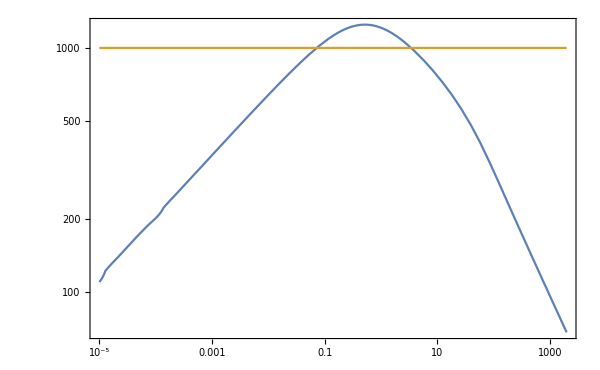

```mathematica
gam=0.05;
regime=If[gam≤1,"γ<<1","γ>>1"];

eff=Max[2/gam^(1/4),2];
rcrit=eff^-4;

res=solEqs[gam];
Print["Exact {x_c1,x_max,x_c2}:"]
xLR=xCross[gam,rcrit]
(xcVals[regime]/.{γ->gam,f->eff})//N;
(xMax[regime]/.{γ->gam,f->eff})//N;
Print["Approximate {x_c1,x_max,x_c2}:"]
{%%%⟦1⟧,%%,%%%⟦2⟧}
Print["Error [(Approx-Exact)/Exact]:"]
(%%/%%%%%%)-1

domain=InterpolatingFunctionDomain[res⟦2⟧]//Flatten;

Print["γ_c^RATE"]
{gammaRate[gam,xLR⟦1⟧],gammaRate[gam,xLR⟦-1⟧]}

p1=LogLogPlot[{res⟦1⟧[2/3+dx],res⟦2⟧[2/3+dx]},{dx,10^-5,domain⟦2⟧-2/3},PlotRange->{10^-8,100},PlotStyle->{{Blue,Thick},{Red,Thick}},GridLines->{(xLR-2/3)~Join~{1/gam - 2/3},{rcrit}},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["\\rho/\\rho_{\\phi,i}",Magnification->2]},PlotLegends->Placed[LineLegend[{MaTeX["\\rho_{\\phi}",Magnification->1.7],MaTeX["\\rho_{r}",Magnification->1.7]}],{0.9,0.85}],Epilog->{Inset[Rotate[MaTeX["\\color{black} t=t_\\textrm{max}",Magnification->1.5],90°],Scaled[{.43,.2}]],Inset[Rotate[MaTeX["\\color{black} t=\\Gamma_\\phi^{-1}",Magnification->1.5],90°],Scaled[{.63,.2}]],Inset[Rotate[MaTeX["\\color{black} T=T_c",Magnification->1.5],0°],Scaled[{.08,.55}]],Inset[Rotate[MaTeX[ToString["\\begin{aligned} \\Gamma_\\phi &= "<>ToString[gam]<>"H_i \\end{aligned}"],Magnification->1.3],0°],Scaled[{.13,.9}]]}];

ϕDFns={rϕ[x]/.solsAn[regime,"ϕD"],rr[x]/.solsAn[regime,"ϕD"]}/.{γ->gam,f->eff};
RDFns={rϕ[x]/.solsAn[regime,"RD"],rr[x]/.solsAn[regime,"RD"]}/.{γ->gam,f->eff};
(ϕDFns~Join~RDFns)/.{x->2/3+dx};

p2=LogLogPlot[%,{dx,10^-5,domain⟦2⟧-2/3},PlotStyle->{{Blue,Dashed,Thickness[0.002]},{Red,Dashed,Thickness[0.002]},{Blue,Dotted,Thickness[0.002]},{Red,Dotted,Thickness[0.002]}},PlotRange->{10^-8,100},Frame->True,ImageSize->600,FrameTicks->{{fticksR2[10^-20,10^10,2],fticksRNoLabels[10^-20,10^10,2]},{fticksR[10^-10,10^10,2],fticksRNoLabels[10^-10,10^10,2]}},LabelStyle->16];

Show[p1,p2]

gSS=10;
TC=1000;
HI=eff^2*(Aρ/.gstar->gSS)*TC^2/(3mpl);
TOfx[gam,gSS,HI];
LogLogPlot[{%[2/3+dx],TC},{dx,10^-5,domain⟦2⟧-2/3},Frame->True,FrameLabel->{MaTeX["(t-t_i)H_i",Magnification->2],MaTeX["T [\\mathrm{GeV}]",Magnification->2]}]

Clear[gam,eff,regime,rcrit,res,xLR,domain,ϕDFns,RDFns,p1,p2,gSS,TC,HI]
```